```mathematica
(* Load astronomy_constants.nb first *)
```

```mathematica
(* For jet structure see: lornetz_factor_limit.nb *)
(* NOW: See gamma_jet.nb for complete new jet structure *)
```

```mathematica
(* Set constants and fluid values at r0 *)
```

```mathematica
M=3*msun
rl=G*M/c^2
```

5.967×10^33

442966.

4.42966×10^6

2

30

π/6

3/4

30000

1.×10^14

14.757

8.88685×10^24

```mathematica
(* Set jet solution *)
```

```mathematica
Gamff=Gam0*(r/r0)^(1-nu/2)
Gammhd=sigma0
Gam=1/(1/Gamff+1/Gammhd)
theta=theta0*(r/r0)^(-nu/2)
gdet=r^2*Sin[theta]
gdet0=gdet//.{r->r0}
rho=rho0/(Gam/Gam0*gdet/gdet0)
nden=rho/mb
R=r*Sin[theta]
z=r*Cos[theta]
s=2/nu
MM=0.2
T=(z/R)^(-(2-nu))
Bphihat=Bphihat00*(-nu*s*MM*R^(nu-2)*T^((nu-1)/nu))
fun=Bphihat//.{r->r0}
sols=Solve[fun==-B0,Bphihat00]
Bphihat0=sols[[1,1,2]]
Bphihat=Bphihat0*(-nu*s*MM*R^(nu-2)*T^((nu-1)/nu))
```

0.000140297 r^(5/8)

30000

1/(1/30000+7127.74/r^(5/8))

162.7/r^(3/8)

r^2 Sin[162.7/r^(3/8)]

9.81096×10^12

(2.8956×10^14 (1/30000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2

(1.74377×10^38 (1/30000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2

r Sin[162.7/r^(3/8)]

r Cos[162.7/r^(3/8)]

8/3

0.2

1/(Cot[162.7/r^(3/8)]^(5/4))

-(0.4 Bphihat00)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

-5.88551×10^-9 Bphihat00

{{Bphihat00→1.69909×10^22}}

1.69909×10^22

-(6.79635×10^21)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

```mathematica
(* equipartition temperature for just baryons *)
```

```mathematica
Te=Bphihat^2/(8*Pi)/(2*kb*nden)
Plot[Te,{r,r0,100*rl}]
```

(3.81686×10^19 r^2 Sin[162.7/r^(3/8)])/((1/30000+7127.74/r^(5/8)) (1/(Cot[162.7/r^(3/8)]^(5/4)))^(2/3) (r Sin[162.7/r^(3/8)])^(5/2))

-Graphics-

```mathematica
(* field strength *)
```

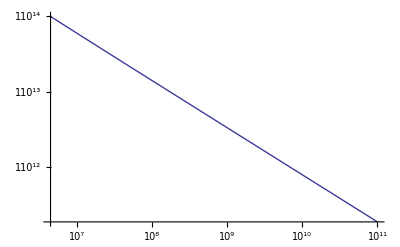

```mathematica
LogLogPlot[-Bphihat,{r,r0,10^(11)}]
```

```mathematica
(* rest-mass density in baryons *)
```

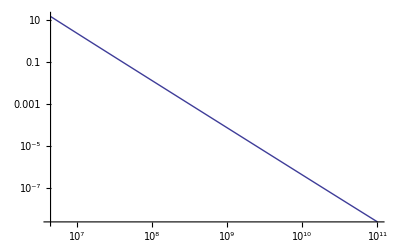

```mathematica
LogLogPlot[rho,{r,r0,10^(11)}]
```

```mathematica
(* number density of baryons *)
```

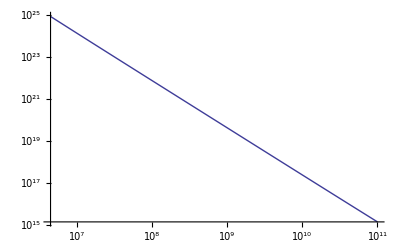

```mathematica
LogLogPlot[nden,{r,r0,10^(11)}]
```

```mathematica
(* Lorentz factor *)
```

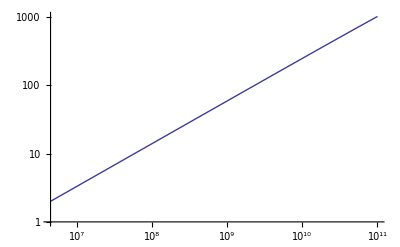

```mathematica
LogLogPlot[Gam,{r,r0,10^(11)}]
```

```mathematica
(* Half-opening angle in degrees *)
```

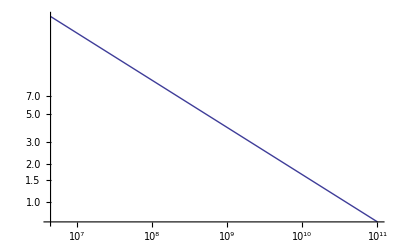

```mathematica
LogLogPlot[180/Pi*theta,{r,r0,10^(11)}]
```

```mathematica
(* Choose radius to solve equations at *)
```

```mathematica
myrconst={r->10^14}
```

{r→100000000000000}

```mathematica
(* Find equipartition temperature in reconnection layer *)
```

```mathematica
Pbaryon=rho*Tg*kb/mb
Pe=Pbaryon
urad=arad*Tg^4
Prad=arad*Tg^4/3
Ppairs=arad*Tg^4*7/12*Exp[-me*c^2/(kb*Tg)]
(*Ppairs=arad*Tg^4*7/12*)
Pg=Prad+Ppairs+Pbaryon+Pe
Ug=(Ppairs+Prad)/(4/3-1)+(Pe+Pbaryon)/(5/3-1)
Pb=Bphihat^2/(8*Pi)
eqT=(Pg==Pb)//.myrconst
sols=FindRoot[eqT,{Tg,10^9},WorkingPrecision->20]
(*myTg=sols[[4,1,2]]*)
myTg=sols[[1,2]]
```

(2.40755×10^22 (1/30000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

(2.40755×10^22 (1/30000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

7.56593×10^-15 Tg^4

2.52198×10^-15 Tg^4

4.41346×10^-15 ⅇ^(-5.92986×10^9/Tg) Tg^4

2.52198×10^-15 Tg^4+4.41346×10^-15 ⅇ^(-5.92986×10^9/Tg) Tg^4+(4.8151×10^22 (1/30000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

3 (2.52198×10^-15 Tg^4+4.41346×10^-15 ⅇ^(-5.92986×10^9/Tg) Tg^4)+(7.22265×10^22 (1/30000+7127.74/r^(5/8)) Tg Csc[162.7/r^(3/8)])/r^2

(1.83786×10^42)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(2/3) (r Sin[162.7/r^(3/8)])^(5/2))

2.42134×10^-7 Tg+2.52198×10^-15 Tg^4+4.41346×10^-15 ⅇ^(-5.92986×10^9/Tg) Tg^4==2.47183×10^17

FindRoot::precw: The precision of the argument function (2.421338440673224`*^-7 Tg + 2.521978193401107`*^-15 Tg^4 + 4.413461838451938`*^-15 ⅇ^-5.929856910549338`*^9/Tg Tg^4 == 2.4718338473769715`*^17) is less than WorkingPrecision (20.).

{Tg→9.9499176636702171864×10^7}

9.9499176636702171864×10^7

```mathematica
(* Look at pressures at equipartition temperature *)
```

```mathematica
Pbaryon//.{Tg->myTg}//.myrconst
Prad//.{Tg->myTg}//.myrconst
Ppairs//.{Tg->myTg}//.myrconst
Pg//.{Tg->myTg}//.myrconst
Pb//.{Tg->myTg}//.myrconst
```

12.0461

2.47183×10^17

5.66747×10^-9

2.47183×10^17

2.47183×10^17

```mathematica
(* Timescale for photon diffusion (cooling timescale) across layer vs transit time through layer = light crossing time *)
```

```mathematica
(*
2 regimes:
1) optically thin inefficient cooling
2) very optically thick
*)
(* dominate cooling: synchrotron and Compton *)
```

```mathematica
1/(4/3-1)
```

3

```mathematica
(* Use temperature from above *)
```

```mathematica
newTgconst={Tg->myTg}
```

{Tg→9.9499176636702171864×10^7}

```mathematica
(* Set number densities of pairs, total electrons+positrons, and skin depths *)
```

```mathematica
npairs=(7/4*arad*Tg^4/(kb*Tg))*Exp[-me*c^2/(kb*Tg)]
ndentot=nden+npairs//.newTgconst//.myrconst
omegape=Sqrt[4*Pi*ndentot*q^2/me]
omegapi=Sqrt[4*Pi*nden*q^2/mp]
de=c/omegape
di=c/omegapi
j1=c*B0/(4*Pi*c)*omegape
j2=q*nden*vd
```

95.8991 ⅇ^(-5.92986×10^9/Tg) Tg^3

8.76878×10^8

1.67045×10^9

1.73842×10^22 √(((1/30000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2)

17.9468

(1.72451×10^-12)/(√(((1/30000+7127.74/r^(5/8)) Csc[162.7/r^(3/8)])/r^2))

1.3293×10^22

(8.37516×10^28 (1/30000+7127.74/r^(5/8)) vd Csc[162.7/r^(3/8)])/r^2

```mathematica
(* Look at number densities *)
```

```mathematica
npairs//.newTgconst//.myrconst
nden//.newTgconst//.myrconst
```

1.23767

8.76878×10^8

```mathematica
(* Compute Larmor radius *)
```

```mathematica
Ee=3/2*kb*Tg//.{Tg->myTg}
ve=Sqrt[Ee*2/me]//.myrconst
wge=q*(-Bphihat)/(me*c)
Rl=ve/wge//.myrconst
```

2.06062×10^-8

6.72619×10^9

(1.19528×10^29)/((1/(Cot[162.7/r^(3/8)]^(5/4)))^(1/3) (r Sin[162.7/r^(3/8)])^(5/4))

1.53442×10^-7

```mathematica
(* compute ptical depth to electron scattering within Petschek layer *)
tau=sigmat*ndentot*de
```

1.04664×10^-14

```mathematica
(* Compare annihilation time to plasma time to see if pairs included as charge carriers for plasma frequency *)
```

```mathematica
Tann=1/(n*sigmat*c)
omegap=Sqrt[4*Pi*n*q^2/me]
Tp=2*Pi/omegap
myn=Solve[Tann==Tp,n][[1,1,2]]
myn*me*mp/me
paireden=myn*me*c^2
```

(5.01542×10^13)/n

56411. √n

0.000111382/(√n)

2.0276×10^35

3.39141×10^11

1.66002×10^29

```mathematica
(* Obtain classical critical field strength *)
```

```mathematica
Solve[paireden==Bit^2/(8*Pi),Bit]
```

{{Bit→-2.04257×10^15},{Bit→2.04257×10^15}}

```mathematica
(* estimate quantum correction *)
```

```mathematica
2*10^15/137.
```

1.45985×10^13

```mathematica
(* Compare number density with classical electron density *)
```

```mathematica
1/(4*Pi/3*radiuse^3)
```

1.06729×10^37

```mathematica
(* so similar *)
```

```mathematica
(* Estimate resistivity *)
```

```mathematica
(* q nden v_d = q j = q E/etaprime *)
```

```mathematica
(*
etaprime=me/(nden*q^2)/taucoll
eta=etaprime*c^2/(4*Pi)
lambdamfp=
eta=de^2/(lambdamfp)*ve
*)
```

```mathematica
(* or: eE = F = v_d/c urad sigmaT *)
```

```mathematica
(* check units *)
```

```mathematica
E0=MMM*LL^2/S^2
(LL/S/(1/S))^2*E0/LL^3*LL^2/(LL/S)
```

(LL^2 MMM)/S^2

(LL^2 MMM)/S

```mathematica
(* Get SP and Spitzer resistivity and corresponding SP lengths across layer *)
```

```mathematica
(*etaprime=urad*sigmat/(ndentot*q^2*c)//.newTgconst//.myrconst*)
eta=(4/3)*(c/omegape)^2/me*urad*sigmat/c//.newTgconst//.myrconst
etaspitzer=c*radiuse*(kb*Tg/(me*c^2))^(-3/2)*20//.newTgconst//.myrconst
L=R//.newTgconst//.myrconst
Va=c*(-Bphihat)/Sqrt[rho*c^2+Ug+Pg+Bphihat^2]//.newTgconst//.myrconst
deltasp=Sqrt[L*eta/Va]//.newTgconst//.myrconst
deltaspitzer=Sqrt[L*etaspitzer/Va]//.newTgconst//.myrconst
```

5.8167×10^12

77.7257

9.14929×10^10

2.78452×10^10

4.37177×10^6

15.9809

```mathematica
(* Sweet Parker optical depth across layer and along layer *)
```

```mathematica
tausp=sigmat*ndentot*deltasp
tauL=sigmat*ndentot*L
```

2.54958×10^-9

0.0000533579

```mathematica
(* Compare photon diffusion time across layer and transit time along layer *)
```

```mathematica
TdiffacrossSP = tausp*deltasp/c//.newTgconst//.myrconst
Ttransit=L/Va//.newTgconst//.myrconst
```

3.71797×10^-13

3.28577

```mathematica
(* So photons leak out and cool layer before transiting fluid is heated *)
```

```mathematica
(* Compute lindquist number *)
```

```mathematica
Lindquist=L*Va/eta//.newTgconst//.myrconst
```

4.37986×10^8

```mathematica
(* Compare size of Petschek and SP layers *)
```

```mathematica
de/deltasp
de/deltaspitzer
```

4.10516×10^-6

1.12302

```mathematica
(* So SP much larger as is normal *)
```

```mathematica
de
```

17.9468

```mathematica
(* Check resistivity from Plasma book *)
```

```mathematica
Tev=kb*Tg/ergPmev*10^6
lnL=20
etaprimebook=10^(-14)*lnL*(Tev)^(-3/2)//.newTgconst//.myrconst
etabook=etaprimebook*c^2/(4*Pi)
```

0.0000861739 Tg

20

2.51905×10^-19

18.0164

```mathematica
(* So similar to Spitzer we wrote down *)
```

```mathematica
(* Compute optical depth to baryon-electron scattering *)
```

```mathematica
Tb=10^4
sigmac=sigmat/(kb*Tb/(me*c^2))^2
tau=L*nden*sigmac//.myrconst
```

10000

2.33862×10^-13

1.87624×10^7

```mathematica
(* So for any reasonable temperature baryons and electrons are significantly coupled due to high density still *)
```

```mathematica
sigmaatr=(-Bphihat)^2/(rho*c^2)//.myrconst
sigmaatr=(-Bphihat)^2/(rho*c^2)//.{r->10*r0}
```

4.74711×10^12

7.61932×10^6